```mathematica
eegYesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/EEGyes_signal.mat"];
numSamplesEegYes = Dimensions[eegYesMatlab][[3]];
eegYesRaw =  Table[Transpose[eegYesMatlab[[1,1,x]]],{x,numSamplesEegYes}];

eegNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/EEGno_signal.mat"];
numSamplesEegNo = Dimensions[eegNoMatlab][[3]];
eegNoRaw =  Table[Transpose[eegNoMatlab[[1,1,x]]],{x,numSamplesEegNo}];



eegStandardLengthYes={};
If[Dimensions[eegYesRaw [[#]]][[2]]==5102,AppendTo[eegStandardLengthYes,Transpose@Drop[Transpose@eegYesRaw [[#]],-1]], AppendTo[eegStandardLengthYes,eegYesRaw [[#]]]]&/@Range[numSamplesEegYes];

eegStandardLengthNo={};
If[Dimensions[eegNoRaw[[#]]][[2]]==5102,AppendTo[eegStandardLengthNo,Transpose@Drop[Transpose@eegNoRaw[[#]],-1]], AppendTo[eegStandardLengthNo,eegNoRaw[[#]]]]&/@Range[numSamplesEegNo];
```

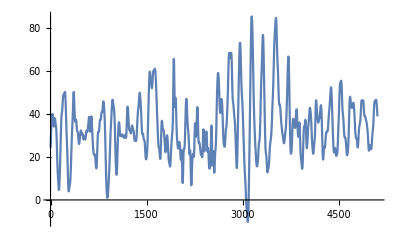

```mathematica
ListLinePlot[eegStandardLengthNo[[1,1]]]
```

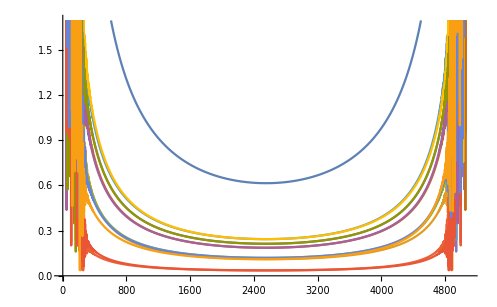

```mathematica
testFourier = Abs@Fourier@eegStandardLengthNo[[1]];
ListLinePlot@testFourier
```

210.056+2 (209.847 Cos[ω]+209.245 Cos[2 ω]+208.257 Cos[3 ω]+206.894 Cos[4 ω]+7766)
 |  |  |  |

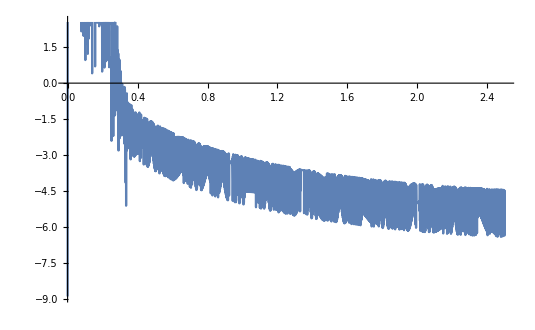

```mathematica
testPSD = PowerSpectralDensity[eegStandardLengthNo[[1,1]],ω]
Plot[Evaluate@Log@testPSD,{ω,0,2.5}]
```

```mathematica
testFourierLowF = ListLinePlot@Abs[Fourier[eegStandardLengthNo[1,1]]]^2
```

Fourier::fftl: Argument {{{24.3107,25.2751,26.2616,27.258,28.2512,29.2283,30.1769,31.0859,«35»,35.9806,35.52,35.1038,34.7455,34.4562,34.2444,34.1155,«5051»},«11»,{«1»}},«29»}[1,1] is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument «1» is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

ListLinePlot::lpn: Abs[Fourier[{{{24.3107,25.2751,26.2616,27.258,28.2512,29.2283,30.1769,«37»,35.52,35.1038,34.7455,34.4562,34.2444,34.1155,«5051»},«11»,{-9.37533,«49»,«5051»}},«29»}[«1»]]] is not a list of numbers or pairs of numbers.

ListLinePlot[Abs[Fourier[{{1},28,{{-43.0957,5099,-71.6509},11,{1}}}[1,1]]]]^2
 |  |  |  |

```mathematica
fc = 500
samplingTime = 1/fc
fbin = fc/5102//N
signalTime=samplingTime*5102//N
```

500

1/500

0.0980008

10.204

30

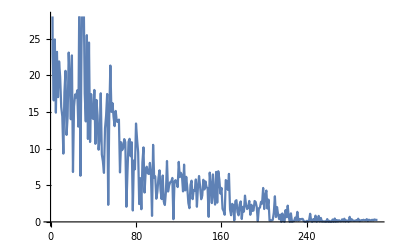

```mathematica
fTarget = 30
ListLinePlot@Take[#,Round[fTarget/fbin]]&@(Log@(Abs@Fourier@eegStandardLengthNo[[1,1]])^2)
```

```mathematica
getFourierCoef[signal_List,targetFrequency_Real] :=Take[#,Round[targetFrequency/(500/Length[signal])]]&@(Abs@Fourier@signal)^2
```

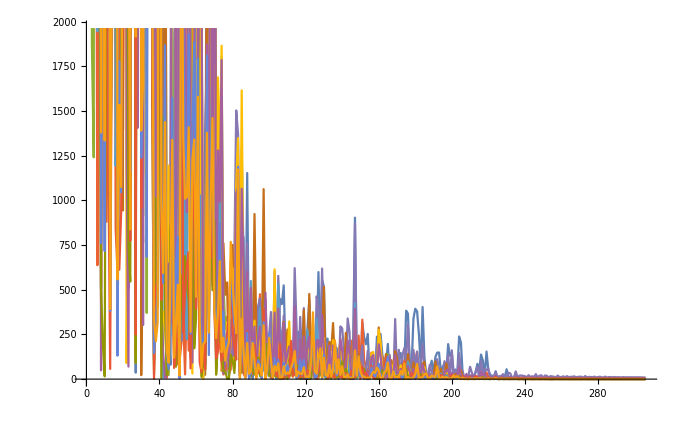

```mathematica
powerSpectrumTest = Table[getFourierCoef[eegStandardLengthNo[[4,channel]],30],{channel,13}];
ListLinePlot[powerSpectrumTest]
```

```mathematica
ArrayPlot[{getFourierCoef[eegStandardLengthNo[[4,1]],30],getFourierCoef[eegStandardLengthNo[[4,2]],30]}]
```

ArrayPlot::mat: Argument {getFourierCoef[{-19.3367,-18.897,-18.4878,-18.0993,-17.722,-17.3468,-16.9657,«37»,8.54822,8.73546,8.86909,8.95536,9.00093,9.0125,«5051»},30],getFourierCoef[{«18»,«49»,«5051»},«2»]} at position 1 is not a list of lists.

ArrayPlot[{getFourierCoef[{-19.3367,-18.897,-18.4878,-18.0993,-17.722,-17.3468,5089,-22.2663,-20.9728,-19.6318,-18.2462,-16.8198,-15.3574},30],1}]
 |  |  |  |